# Метод на най-малките квадрати (МНМК)

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
1. Да се състави таблицата (x_k, g(x_k)), където
x_k =  -b + k(0.1), k = OverBar[0,10],   g(x) = ⅇ^(((a+1)x)/10)
Търси се апроксимацията в точката s = -b + (0.17)a + 0.01. За тази цел:
2. Да се построи полином на ленейна регресия по получената таблица.
3. Да се построи полином на квадратична регресия по получената таблица.
4. Да се построи полином на кубична регресия по получената таблица.
5. Да се пресметне апроксимацията, използвайки всеки един от построените полиноми (общо 3).
6. Да се оцени грешката за всяка от получените апроксимации.
7. Да се направи сравнение между трите резултата.

## Генериране на данни

```mathematica
xt = Table[-8+k*0.1, {k, 0, 10}]
```

{-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.}

```mathematica
f[x_] := ⅇ^((1x)/10)
yt = f[xt]
```

{0.449329,0.453845,0.458406,0.463013,0.467666,0.472367,0.477114,0.481909,0.486752,0.491644,0.496585}

```mathematica
P = Length[xt]
```

11

### Визуализация

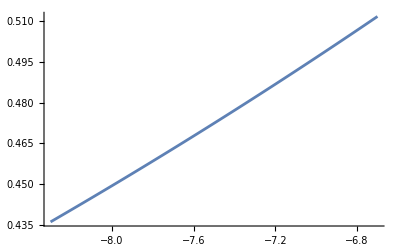

```mathematica
grf = Plot[f[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}]
```

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, P}];
```

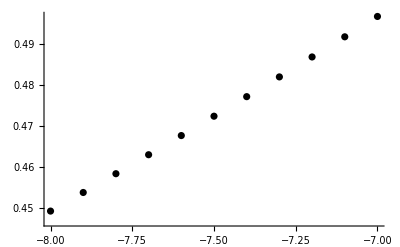

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

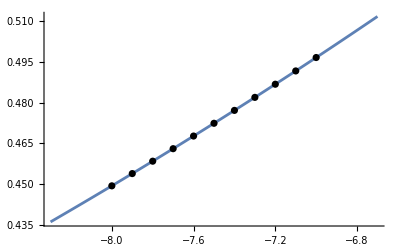

```mathematica
Show[grf, grp]
```

## Линейна регресия

### Попълваме таблицата

```mathematica
xt^2
```

{64.,62.41,60.84,59.29,57.76,56.25,54.76,53.29,51.84,50.41,49.}

```mathematica
yt*xt
```

{-3.59463,-3.58537,-3.57557,-3.5652,-3.55426,-3.54275,-3.53064,-3.51794,-3.50462,-3.49067,-3.4761}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-82.5

```mathematica
∑_(i=1)^P yt[[i]]
```

5.19863

```mathematica
∑_(i=1)^P xt[[i]]^2
```

619.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-38.9378

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]]}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]};
```

```mathematica
LinearSolve[A,b]
```

{0.826983,0.0472507}

### Съставяме полинома

```mathematica
P1[x_] := 0.49398 + 0.0365801x
```

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x}, x]
```

0.826983+0.0472507 x

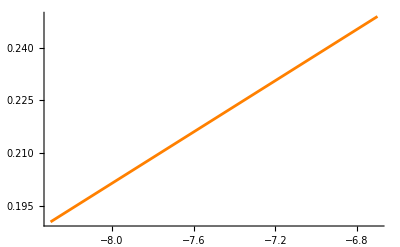

```mathematica
grfP1 = Plot[P1[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Orange]
```

```mathematica
Show[grf, grp, grfP1]
```

-Graphics-

```mathematica
P1[-8.25]
```

0.192194

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.438235

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P1[xt[[i]]])^2)
```

0.839093

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P1[-5.97]]
```

0.274864

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{64.,62.41,60.84,59.29,57.76,56.25,54.76,53.29,51.84,50.41,49.}

```mathematica
yt*xt
```

{-3.59463,-3.58537,-3.57557,-3.5652,-3.55426,-3.54275,-3.53064,-3.51794,-3.50462,-3.49067,-3.4761}

```mathematica
xt^3
```

{-512.,-493.039,-474.552,-456.533,-438.976,-421.875,-405.224,-389.017,-373.248,-357.911,-343.}

```mathematica
xt^4
```

{4096.,3895.01,3701.51,3515.3,3336.22,3164.06,2998.66,2839.82,2687.39,2541.17,2401.}

```mathematica
yt*xt^2
```

{28.7571,28.3245,27.8894,27.452,27.0124,26.5706,26.1268,25.6809,25.2332,24.7838,24.3327}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-82.5

```mathematica
∑_(i=1)^P yt[[i]]
```

5.19863

```mathematica
∑_(i=1)^P xt[[i]]^2
```

619.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-38.9378

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-4665.38

```mathematica
∑_(i=1)^P xt[[i]]^4
```

35176.1

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

292.163

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]],  ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
```

```mathematica
LinearSolve[A,b]
```

{0.959627,0.0826855,0.00236232}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2}, x]
```

0.959627+0.0826855 x+0.00236232 x^2

### Съставяме полинома

```mathematica
P2[x_] := 0.757812 - 0.0987443x + 0.00365672 x^2
```

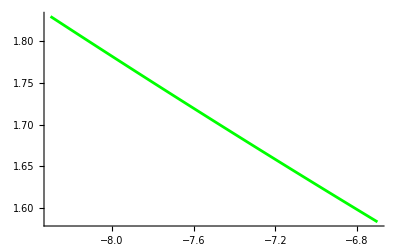

```mathematica
grfP2 = Plot[P2[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Green]
```

```mathematica
Show[grf,grp,grfP1, grfP2]
```

-Graphics-

```mathematica
P2[-8.25]
```

1.82134

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.438235

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P2[xt[[i]]])^2)
```

4.091

#### Истинска грешка

```mathematica
Abs[f[-8.25] - P2[-8.25]]
```

1.3831

## Кубична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{64.,62.41,60.84,59.29,57.76,56.25,54.76,53.29,51.84,50.41,49.}

```mathematica
yt*xt
```

{-3.59463,-3.58537,-3.57557,-3.5652,-3.55426,-3.54275,-3.53064,-3.51794,-3.50462,-3.49067,-3.4761}

```mathematica
xt^3
```

{-512.,-493.039,-474.552,-456.533,-438.976,-421.875,-405.224,-389.017,-373.248,-357.911,-343.}

```mathematica
xt^4
```

{4096.,3895.01,3701.51,3515.3,3336.22,3164.06,2998.66,2839.82,2687.39,2541.17,2401.}

```mathematica
yt*xt^2
```

{28.7571,28.3245,27.8894,27.452,27.0124,26.5706,26.1268,25.6809,25.2332,24.7838,24.3327}

```mathematica
yt*xt^3
```

{-230.056,-223.763,-217.537,-211.381,-205.294,-199.28,-193.338,-187.471,-181.679,-175.965,-170.329}

```mathematica
xt^5
```

{-32768.,-30770.6,-28871.7,-27067.8,-25355.3,-23730.5,-22190.1,-20730.7,-19349.2,-18042.3,-16807.}

```mathematica
xt^6
```

{262144.,243087.,225200.,208422.,192700.,177979.,164206.,151334.,139314.,128100.,117649.}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-82.5

```mathematica
∑_(i=1)^P yt[[i]]
```

5.19863

```mathematica
∑_(i=1)^P xt[[i]]^2
```

619.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-38.9378

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-4665.38

```mathematica
∑_(i=1)^P xt[[i]]^4
```

35176.1

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

292.163

```mathematica
∑_(i=1)^P xt[[i]]^5
```

-265683.

```mathematica
∑_(i=1)^P xt[[i]]^6
```

2.01014×10^6

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^3
```

-2196.09

### Решаваме системата

```mathematica
A= ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5}, {∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5, ∑_(i=1)^P xt[[i]]^6}}); b = {∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]^2, ∑_(i=1)^P yt[[i]]*xt[[i]]^3};
```

```mathematica
LinearSolve[A,b]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{11.,-82.5,619.85,-4665.38},{-82.5,619.85,-4665.38,35176.1},{619.85,-4665.38,35176.1,-265683.},{-4665.38,35176.1,-265683.,2.01014×10^6}} may contain significant numerical errors.

{0.992741,0.0959589,0.00413397,0.0000787398}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2,x^3}, x]
```

0.992741+0.0959589 x+0.00413398 x^2+0.0000787402 x^3

### Съставяме полинома

```mathematica
P3[x_] :=0.907125 + 0.15153x + 0.00987189 x^2 + 0.000243732 x^3
```

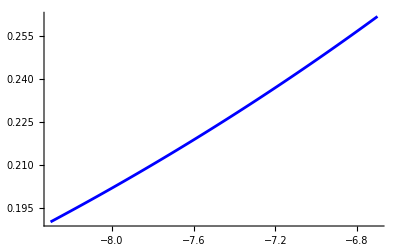

```mathematica
grfP3 = Plot[P3[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle-> Blue]
```

```mathematica
Show[grf, grp, grfP1,grfP2, grfP3]
```

-Graphics-

### Намиране на приближена стойност (s = -b + (0.17)a + 0.01)

```mathematica
s = -8 + 0.17  + 0.01
```

-7.82

```mathematica
P3[-8.25]
```

0.192049

За сравнение истинската стойност

```mathematica
f[-8.25]
```

0.438235

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P3[xt[[i]]])^2)
```

0.825992

#### Истинска грешка

```mathematica
Abs[f[-8.25] - P3[-8.25]]
```

0.246186